## Intro: geometrical rules

```mathematica
(* silver numbers *)
Ag[n_]:=Ag[n]=2Ag[n-1]+Ag[n-2];
Ag[0]=0;
Ag[1]=1;
```

The silver numbers verify
A_(n+2)=2 A_(n+1)+A_n
with S_0=0,S_1=1.
This translates into the inflation rule
s → w
w → wsw (instead of ws for Fibonacci)

```mathematica
(* Fibonacci substitution system *)
NestList[StringReplace[#,{"s"->"w","w"->"ws"}]&,"s",6]
StringCount[%,"w"]
```

{s,w,ws,wsw,wswws,wswwswsw,wswwswswwswws}

{0,1,1,2,3,5,8}

```mathematica
(* Silver substitution system *)
NestList[StringReplace[#,{"s"->"w","w"->"wsw"}]&,"s",6]
StringCount[%,"w"]
StringCount[%%,"s"]
```

{s,w,wsw,wswwwsw,wswwwswwswwswwwsw,wswwwswwswwswwwswwswwwswwswwwswwswwswwwsw,wswwwswwswwswwwswwswwwswwswwwswwswwswwwswwswwwswwswwswwwswwswwwswwswwswwwswwswwwswwswwwswwswwswwwsw}

{0,1,2,5,12,29,70}

{1,0,1,2,5,12,29}

```mathematica
(* we can also generate the chain by cut and project *)
δ=√2-1;
n=2;
test[i_,n_]:=If[Mod[Ag[n+1]i,Ag[n]+Ag[n+1]]≥Ag[n],w,s];
test[#,n]&/@Range[Ag[n]+Ag[n+1]]
```

{w,w,s,w,w,w,s}

This imposes p_n=A_n, q_n=A_(n+1).
If the A_nwere the Fibonacci numbers, we would have had p_n+q_n=A_(n+2). Here the sum (ie the total number of sites) is not a silver number.
Hence, the renormalization scheme of Niu and Nori does not apply.

However, if we consider the substitution rule
s → wsw
w → ws
The associated irrational is
1/δ=√2-1.

```mathematica
(* 1/√2 substitution system *)
NestList[StringReplace[#,{"s"->"wsw","w"->"ws"}]&,"w",6]
StringCount[%,"w"]
StringCount[%%,"s"]
```

{w,ws,wswsw,wswswwswswws,wswswwswswwswswswwswswwswswsw,wswswwswswwswswswwswswwswswswwswswwswswwswswswwswswwswswswwswswwswswws,wswswwswswwswswswwswswwswswswwswswwswswwswswswwswswwswswswwswswwswswwswswswwswswwswswswwswswwswswswwswswwswswwswswswwswswwswswswwswswwswswwswswswwswswwswswswwswswwswswsw}

{1,1,3,7,17,41,99}

{0,1,2,5,12,29,70}

then we readily check that the number of strong bonds is a silver number, while the number of weak bonds is the sum of two consecutive silver numbers:
p_n= A_n
q_n = A_(n-1)+A_n
Hence, p_n+q_n=A_(n+1) and the renormalization scheme applies.
Note that this chain resembles much closely the Fibonacci than the silver chain. Indeed there are no groups of three weak bonds, only groups of two.
The associated irrational is
1/(1+1/δ)= 1/(√2). (hence it has almost the same continued fraction as δ)
It is not a Pisot number since it is not an algebraic integer:

```mathematica
AlgebraicIntegerQ[1/√2]
```

False

## Hamiltonians

### Definitions

```mathematica
(* Silver Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,ρ_]:=Block[{F0=Ag[n],F1=Ag[n+1],F2=Ag[n]+Ag[n+1],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Silver Hamiltonian, in the co-basis, with free bc *)
hcof[n_,ρ_]:=Block[{F0=Ag[n],F1=Ag[n+1],F2=Ag[n]+Ag[n+1],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,2,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Silver Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,ρ_]:=Block[{F0=Ag[n],F1=Ag[n+1],F2=Ag[n]+Ag[n+1],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,2,F0}];
PrependTo[tblw,{1,1+F1}->-1.];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Silver Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,ρ_]:=Block[{F0=Ag[n],F1=Ag[n+1],F2=Ag[n]+Ag[n+1],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,2,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]ρ];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* normal basis *)
jump[i_,n_,ρ_]:=If[Mod[Ag[n+1]i,Ag[n]+Ag[n+1]]≥Ag[n],ρ,1.];

(* Silver Hamiltonian, in the normal basis, with free bc *)
hf[n_,ρ_]:=Block[{F2=Ag[n]+Ag[n+1],tbl,ar},
tbl=Table[{i,i+1}->jump[i,n,ρ],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,ρ_]:=Block[{F2=Ag[n]+Ag[n+1],tbl,ar},
tbl=Table[{i,i+1}->jump[i,n,ρ],{i,1,F2-1}];
(* last coupling is always strong *)
AppendTo[tbl,{1,F2}->1.];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

### Tests

Test if a permutation indeed gives the Toeplitz Hamiltonian

```mathematica
n=4;
q=Ag[n+1];
p=Ag[n];
conum[i_]:=Mod[q i,p+q]+1;
co=conum/@Range[p+q];
perm=Table[DiscreteDelta[i-co[[j]]],{i,p+q},{j,p+q}];
perm.hpn[n,22].Transpose[perm]==hp[n,22]
```

True

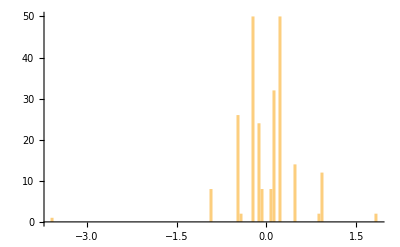

```mathematica
n=6;
enp=Sort@Eigenvalues[ha[n,0.1]];
ena=Sort@Eigenvalues[hp[n,0.1]];

Histogram[ena-enp,100]
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=5,ρ=0.1},
{val,vec}=Eigensystem[hp[i,ρ]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

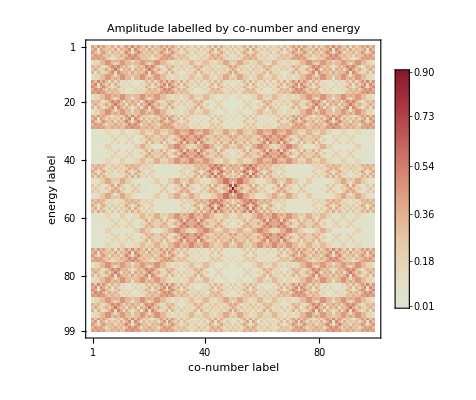

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

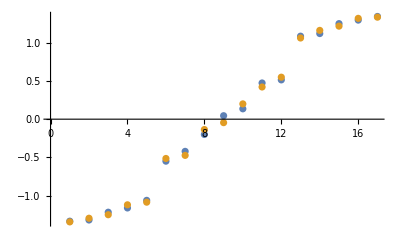

```mathematica
Block[{ρ=.5,vpp,vpa,i=3},
vpp=Sort@Eigenvalues[hp[i,ρ]];
vpa=Sort@Eigenvalues[ha[i,ρ]];
ListPlot[{vpp,vpa},Joined->False,PlotStyle->Thickness[0.005]]
]
```

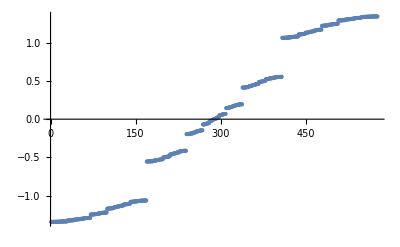

```mathematica
ListPlot[Sort@Eigenvalues[hp[7,0.5]],Joined->False]
```

## Fractal dimensions of the wavefunctions

### Definitions

```mathematica
(* return bands and intensities ordered by increasing energy,for 2 consecutive sizes Ag[n] and Ag[n+1] *)IntBands[n_,ρ_]:=Block[{nN=n+1,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},(*spectres des systèmes de taille i p et anti-p*){vpp,wfp}=Eigensystem[hp[n-2,ρ]];
{vpa,wfa}=Eigensystem[ha[n-2,ρ]];
o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(*intensity*)intp=Abs[wfp]^2;
o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;
intensities=0.5*(intp+inta);
(*spectres des systèmes de taille i+1 p et anti-p*){vppN,wfpN}=Eigensystem[hp[nN-2,ρ]];
{vpaN,wfaN}=Eigensystem[ha[nN-2,ρ]];
o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(*intensity*)intpN=Abs[wfpN]^2;
o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;
intensitiesN=0.5*(intpN+intaN);
(*la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique*)bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{intensities,intensitiesN,bands,bandsN}]
```

```mathematica
(*Averaged q-intensity*)
avInt[intlist_,q_]:=(1/Length[intlist])*Map[Plus@@((#)^q)&,Transpose[intlist]];

(*Compute τx(q) from the averaged q-intensity*)
tauqx[avint_,avintN_]:=-Log[(Plus@@avint)/(Plus@@avintN)]/Log[(Length@avint)/(Length@avintN)];

(* compute the local Dx(q,i) for the local intensities *)WfD[wf_,q_]:=-(q-1)^(-1) Log[Total@(wf^ (2q))]/Log[Length@wf]
```

### Tests

```mathematica
(* local dimensions as a function of the site, integrated over all energies *)
dqi=Block[{ρ=.1,n=8,q=2.,val,vec,int},
{val,vec}=Eigensystem[hp[n,ρ]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
WfD[#,q]&/@Transpose[vec]
];
```

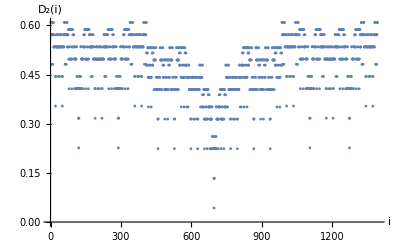

```mathematica
ListPlot[dqi,PlotRange->All,AxesLabel->{"i","D_2(i)"},PlotStyle->PointSize[0.005]]
```

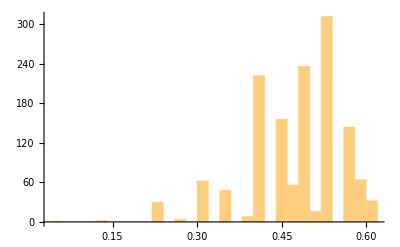

```mathematica
Histogram[dqi,20]
```

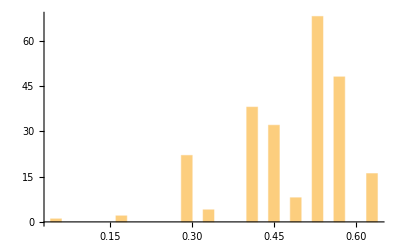

```mathematica
Histogram[dqiN,20]
```

```mathematica
test[Ag[8]+Ag[9]-1]
```

s

```mathematica
(* local dimensions as a function of the energy, integrated over all sites *)
dqa=Block[{ρ=.1,n=8,q=2.,val,vec,int},
{val,vec}=Eigensystem[hcof[n,ρ]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
WfD[#,q]&/@vec
];
```

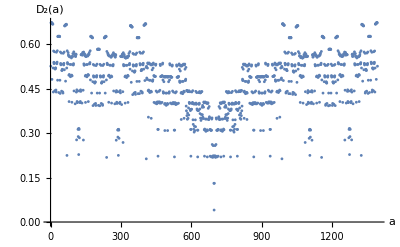

```mathematica
ListPlot[dqa,PlotRange->All,AxesLabel->{"a","D_2(a)"},PlotStyle->PointSize[0.005]]
```

```mathematica
{val,vec}=Eigensystem[hp[n,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
```

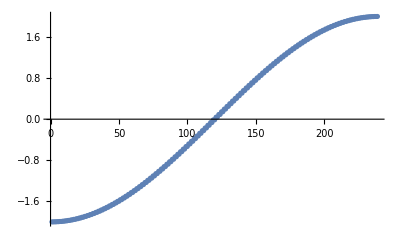

```mathematica
ListPlot[Sort@val]
```

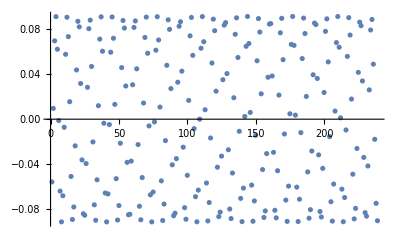

```mathematica
ListPlot[vec[[3]]]
```

## Relations between dimensions

### Definitions

```mathematica
(* return bands and intensities ordered by increasing energy,for 2 consecutive sizes Ag[n] and Ag[n+1] *)IntBands[n_,ρ_]:=Block[{nN=n+1,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},(*spectres des systèmes de taille i p et anti-p*){vpp,wfp}=Eigensystem[hp[n-2,ρ]];
{vpa,wfa}=Eigensystem[ha[n-2,ρ]];
o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(*intensity*)intp=Abs[wfp]^2;
o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;
intensities=0.5*(intp+inta);
(*spectres des systèmes de taille i+1 p et anti-p*){vppN,wfpN}=Eigensystem[hp[nN-2,ρ]];
{vpaN,wfaN}=Eigensystem[ha[nN-2,ρ]];
o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(*intensity*)intpN=Abs[wfpN]^2;
o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;
intensitiesN=0.5*(intpN+intaN);
(*la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique*)bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{intensities,intensitiesN,bands,bandsN}]
```

```mathematica
(*Averaged q-intensity*)
avInt[intlist_,q_]:=(1/Length[intlist])*Map[Plus@@((#)^q)&,Transpose[intlist]];

(*Compute τx(q) from the averaged q-intensity*)
tauqx[avint_,avintN_]:=-Log[(Plus@@avint)/(Plus@@avintN)]/Log[(Length@avint)/(Length@avintN)];

(*Compute τμ(q) from 2 consecutive (Subscript[F,n] and Subscript[F,n+3]) averaged q-intensities*)
tauqmu[avint_,avintN_,bl_,blN_]:=Block[{gammu,gammuN},
(*associated Γ function (bl is the list of bands)*)
gammu=Plus@@((avint) (bl)^-τ);
gammuN=Plus@@((avintN) (blN)^-τ);
τ/.FindRoot[gammu/gammuN-1,{τ,1.}]]

(*Compute spectral τ(qsp)*)
tauspec[qsp_,bl_,blN_]:=Block[{gamSpec,gamSpecN},(*Fractal dimension of the spectrum*)gamSpec=(Length@bl)^-qsp Plus@@((bl)^-τ);
gamSpecN=(Length@blN)^-qsp Plus@@((blN)^-τ);
τ/.FindRoot[gamSpecN/gamSpec-1,{τ,0.5}]]
```

### ρ=0.1

```mathematica
ρ = 0.1;
n = 9;
nN = n -2;
qr = Range[-1., -0.5, .06]~Join~Range[-0.5,0.,.02]~Join~Range[0.,2.,0.21];

(* bands, intensities... *)
{int, intN, bl, blN} = IntBands[n, ρ];
{int2, intN2, bl2, blN2} = IntBands[nN, ρ];

(* list of averaged over i and weighted intensities *)
avints = ParallelMap[avInt[int, #] &, qr];
avintsN = ParallelMap[avInt[intN, #] &, qr];

(* list of averaged over i and weighted intensities *)
avints2 = ParallelMap[avInt[int2, #] &, qr];
avintsN2 = ParallelMap[avInt[intN2, #] &, qr];

(* τx(qr) *)
τx1 = Parallelize@MapThread[tauqx, {avints, avintsN}];
τx2 = Parallelize@MapThread[tauqx, {avints2, avintsN2}];
(* deduce qspec *)
qsp1 = 1 + τx1;
qsp2 = 1 + τx2;

(* compute τ(qspec) *)
τsp1 = ParallelMap[tauspec[#, bl, blN] &, qsp1];
τsp2 = ParallelMap[tauspec[#, bl2, blN2] &, qsp2];

(* compute τμ(qr) *)
τmu1 = Parallelize@MapThread[tauqmu[#1, #2, bl, blN] &, {avints, avintsN}];
τmu2 = Parallelize@MapThread[tauqmu[#1, #2, bl2, blN2] &, {avints2, avintsN2}];

(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp1 = τsp1/(qr - 1);
dxdsp2 = τsp2/(qr - 1);
dmu1 = τmu1/(qr - 1);
dmu2 = τmu2/(qr - 1);

glue[l1_, l2_] := MapThread[{#1, #2} &, {l1, l2}];
```

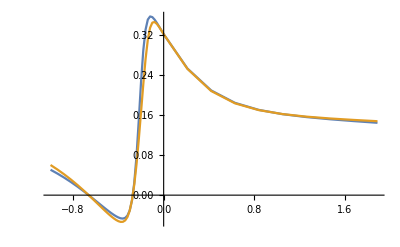

```mathematica
ListPlot[{glue[qr, dxdsp1], glue[qr, dmu1]},Joined->True]
```

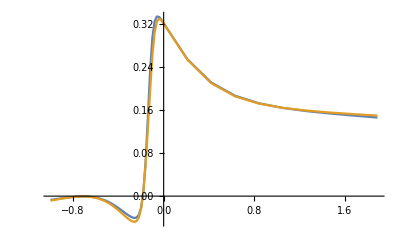

```mathematica
ListPlot[{glue[qr, dxdsp2], glue[qr, dmu2]},Joined->True]
```